# Quantum Teleportation

Referencespaclet:Q3/tutorial/QuantumTeleportation#1175517547 | Quantum Circuit Modelpaclet:Q3/tutorial/QuantumTeleportation#1178477808

Quantum teleportation is a quantum communication protocol to transmit quantum states between remotely separated parties using pre-shared entangled pairs and classical channels. Unlike teleportation which is commonly depicted in science fiction, quantum teleportation does not transfer the object (matter) itself but only information.

Quantum teleportation was first investigated by C. H. Bennet and his collaborators in 1993 [1].

Here we demonstrate the quantum teleportation using the Q3 Application.

QuissoCircuit | Circuit representation of elementary gates
CNOT | Two-qubit controlled-NOT gate
Matrix | Converts QuissoCircuit and operator (or Ket) expressions to the matrix representation in the standard basis.
QuissoExpression | Converts the matrix representation to operator expressions

Functions used in the demonstration of the quantum teleportation protocol.

## References

[1] C. H. Bennet, G. Brassard, C. Crepeau, R. Jozsa, A. Peres, and W. K. Wootters, "Teleporting an Unknown Quantum State via Dual Classical and Einstein-Podolsky-Rosen Channels," Physical Review Letters 70 (13), 1895 (1993).

## Quantum Circuit Model

Start with loading the package

```mathematica
<<Q3`
```

Choose the symbol to denote the Qubitspaclet:Q3/ref/Qubits.

```mathematica
Let[Qubit,S]
```

Bob chooses randomly a state to teleport to Alice, and prepare the third Qubitpaclet:Q3/ref/Qubit Spaclet:Global/ref/S[3,Nonepaclet:ref/None] in it.

```mathematica
in=Basis[S[3]].Normalize@RandomReal[{-1,1},2]
```

0.26409 ␣-0.964498 1_S_3

Check the normalization of the state.

```mathematica
Dagger[in]**in//Chop
```

1.

Here is the quantum circuit of teleportation.

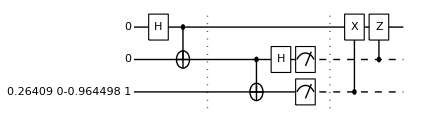

```mathematica
qc=QuissoCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],
S[2,6],{Measurement[S[2]],Measurement[S[3]]},"Separator",
ControlledU[S[3],S[1,1]],
ControlledU[S[2],S[1,3]]
]
```

Convert the quantum circuit (represented by QuissoCircuitpaclet:Q3/ref/QuissoCircuit) to Quisso expression by means of either QuissoExpresssionpaclet:Q3/ref/QuissoExpresssion or Matrixpaclet:Q3/ref/Matrix (usually faster).

```mathematica
outAll=QuissoExpression[qc]//Simplify
```

0.26409 ␣-0.964498 1_S_1

Let us examine the state in Alice’s qubit (S[1,None]).

```mathematica
out=Last@QuissoFactor[outAll,S[{2,3}]]//Simplify;
out//LogicalForm
```

0.26409 0_S_1-0.964498 1_S_1

You can see the state is the same as the input state. In case, there is irrelevant overall phase factor, let us check the fidelity.

```mathematica
Fidelity[Matrix@in,Matrix@out]
```

1.

As the quantum teleportation is deterministic, Bob’s Bell measurement result does not matter. For the heuristic purposes, let us take a look at Bob’s measurement statistics.

```mathematica
val=Table[
out=QuissoExpression[qc]//Simplify;
Readout[out,S[{2,3}]],
{100}
];
Histogram3D[val]
```

-Graphics3D-

In the above example, the statistical distribution is not completely uniform. You can try with increased number of repetitions. However, the point is that regardless of the statistical distribution of the measurement outcomes, the teleportation is always successful.

Related Guides

Quisso Package Guide

Related Tutorials

QuissoCircuit Usage Examples

Quisso: Quick Start

Related Wolfram Education Group Courses

An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/

The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/